```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tep/Dropbox/Mon Mac (MBP-de-admin)/Documents/GitHub/Linear-Galactic-Disk-Theory/code/nb

## Growth rate

#### Import data

#### Diffusion coefficients

```mathematica
tabqx=Import["../data/Dump_Growth_Rate_eps0_2.hf5",{"Datasets","tabqx"}];
tabGR=Import["../data/Dump_Growth_Rate_eps0_2.hf5",{"Datasets","tabGR"}]; 

GRTable=Partition[{tabqx,tabGR}//Transpose//Flatten,3];
```

#### Plot data

```mathematica
(*Generic options for the plots.*)
fontname = "Didot";
fontsize = 12;
basestyleplot = {FontFamily -> fontname,FontSize->fontsize};
labelstyleplot = {FontFamily -> fontname, FontSize -> fontsize};
imagesize = Large;(*350;*)
(*Making the plot.*)
(*Range of the plot.*)
qmin = 0.1;
qmax = 1.0;
xmin = 0.1;
xmax = 1.0;
zmin =0;
zmax = 15;
(*Axes of the plot.*)
ax = Row[{Style["q = ",fontname,fontsize],Style[FractionBox["Mdisk","Mdisk+MDH"]//DisplayForm,fontname,fontsize]}];
ay =  Row[{Style["x = ",fontname,fontsize],Style[FractionBox["Mdisk","Mdisk+Mbulb"]//DisplayForm,fontname,fontsize]}];
(*.*)
axstyle = {Black,Thickness[0.003]};
tickstyle = {Black,Thickness[0.003]};
(*.*)
qticks = {{0.1,"0.1"},{0.2,""},{0.3,""},{0.4,""},{0.5,"0.5"},{0.6,""},{0.7,""},{0.8,""},{0.9,""},{1.0,"1.0"}};
xticks =  {{0.1,"0.1"},{0.2,""},{0.3,""},{0.4,""},{0.5,"0.5"},{0.6,""},{0.7,""},{0.8,""},{0.9,""},{1.0,"1.0"}};
zticks={1,2,3,4,5,6,7,8,9,10};
```

```mathematica
pGR=ListContourPlot[GRTable,Contours->30,PlotRange->{All,All,{zmin,zmax}},ColorFunction->"Rainbow",FrameLabel->{ax,ay},BaseStyle->basestyleplot,LabelStyle->labelstyleplot,PlotLegends->Placed[BarLegend[{(ColorData["Rainbow"][#]&),{zmin,zmax}},LegendLabel->"Growth rate",Method->{FrameStyle->axstyle,TicksStyle->tickstyle,Ticks->{{0,"0"},(*{0.25,""},{0.5,"0.5"},{0.75,""},*){1,""},(*{1.25,""},{1.5,"1.5"},{1.75,""},*){2,""},{3,""},{4,""},{5,"5"},{6,""},{7,""},{8,""},{9,""},{10,"10"},{11,""},{12,""},{13,""},{14,""},{15,"15"}}}],Above],ImageSize->imagesize,FrameTicks->{qticks,xticks},FrameStyle->{axstyle,axstyle,axstyle,axstyle},PlotRangePadding->None]
pGR=Rasterize[pGR,RasterSize->1000];
pDensGR=ListPlot3D[GRTable,PlotRange->{{qmin,qmax},{xmin,xmax},All},ColorFunction->"Rainbow",BaseStyle->basestyleplot,LabelStyle->labelstyleplot,ImageSize->imagesize,PlotRangePadding->None,AxesLabel->{ax,ay,"GR"}];
pDensGR=Rasterize[pDensGR,RasterSize->1000]
```

-Graphics-

-Graphics-

#### Save data

```mathematica
Export["../graphs/growthRate_eps0_2.png",pGR]
Export["../graphs/growthRate3D_eps0_2.png",pDensGR]
```

../graphs/growthRate_eps0_1.png

../graphs/growthRate3D_eps0_1.png

## Growth rate (x vs α)

#### Import data

#### Diffusion coefficients

```mathematica
tabax=Import["../data/Dump_Growth_Rate_alpha_eps0_2.hf5",{"Datasets","tabax"}];
tabGR=Import["../data/Dump_Growth_Rate_alpha_eps0_2.hf5",{"Datasets","tabGR"}]; 

GRTable=Partition[{tabax,tabGR}//Transpose//Flatten,3];
```

#### Plot data

```mathematica
(*Generic options for the plots.*)
fontname = "Didot";
fontsize = 12;
basestyleplot = {FontFamily -> fontname,FontSize->fontsize};
labelstyleplot = {FontFamily -> fontname, FontSize -> fontsize};
imagesize = 350;
(*Making the plot.*)
(*Range of the plot.*)
amin = 0.0;
amax = 10.0;
xmin = 0.1;
xmax = 1.0;
zmin =0;
zmax = 15;
(*Axes of the plot.*)
ax = Row[{Style["α = ",fontname,fontsize],Style[FractionBox["MDH","Mdisk"]//DisplayForm,fontname,fontsize]}];
ay =  Row[{Style["x = ",fontname,fontsize],Style[FractionBox["Mdisk","Mdisk+Mbulb"]//DisplayForm,fontname,fontsize]}];
(*.*)
axstyle = {Black,Thickness[0.003]};
tickstyle = {Black,Thickness[0.003]};
(*.*)
aticks = {{0,"0"},{1,""},{2,""},{3,""},{4,""},{5,"5"},{6,""},{7,""},{8,""},{9,""},{10,"10"}};
xticks =  {{0.1,"0.1"},{0.2,""},{0.3,""},{0.4,""},{0.5,"0.5"},{0.6,""},{0.7,""},{0.8,""},{0.9,""},{1.0,"1.0"}};
zticks={1,2,3,4,5,6,7,8,9,10};
```

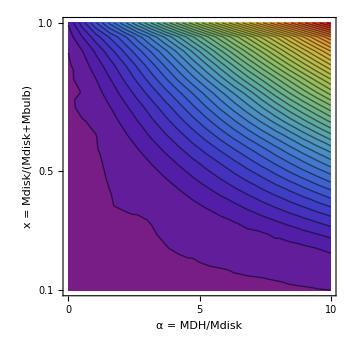

-Graphics-

```mathematica
pGR=ListContourPlot[GRTable,Contours->50,PlotRange->{All,All,{zmin,zmax}},ColorFunction->"Rainbow",FrameLabel->{ax,ay},BaseStyle->basestyleplot,LabelStyle->labelstyleplot,PlotLegends->Placed[BarLegend[{(ColorData["Rainbow"][#]&),{zmin,zmax}},LegendLabel->"Growth rate",Method->{FrameStyle->axstyle,TicksStyle->tickstyle,Ticks->{{0,"0"},{1,""},{2,""},{3,""},{4,""},{5,"5"},{6,""},{7,""},{8,""},{9,""},{10,"10"},{11,""},{12,""},{13,""},{14,""},{15,"15"}}}],Above],ImageSize->imagesize,FrameTicks->{aticks,xticks},FrameStyle->{axstyle,axstyle,axstyle,axstyle},PlotRangePadding->None]
pGR=Rasterize[pGR,RasterSize->1000];
pDensGR=ListPlot3D[GRTable,PlotRange->{{amin,amax},{xmin,xmax},All},ColorFunction->"Rainbow",BaseStyle->basestyleplot,LabelStyle->labelstyleplot,ImageSize->imagesize,PlotRangePadding->None,AxesLabel->{"q","x","GR"}];
pDensGR=Rasterize[pDensGR,RasterSize->1000]
```

```mathematica
Export["../graphs/growthRateAlpha_eps0_2.png",pGR]
Export["../graphs/growthRate3DAlpha_eps0_2.png",pDensGR]
```

../graphs/growthRateAlpha_eps0_2.png

../graphs/growthRate3DAlpha_eps0_2.png